# -Graphics-

# Scientific Computing with Mathematica

## Part (2): Ordinary Differential equations

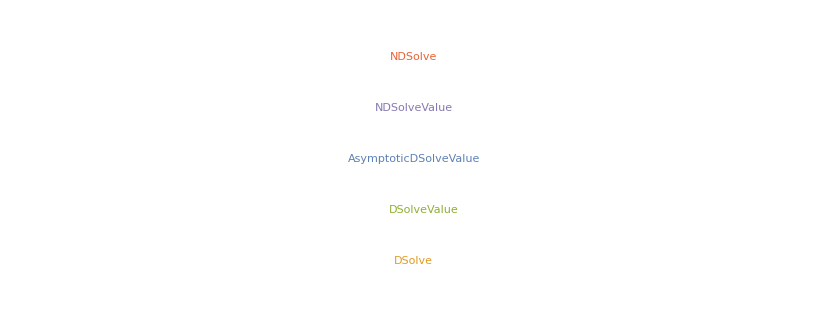

## Outline

### Classification of Ordinary Differential Equations (ODEs)

### Symbolic Solution to ODEs

### Numerical Solution to ODEs

### Asymptotic Solution to ODEs

#### Classification of Differential Equations

The solution method used by DSolve and the nature of the solutions depend heavily on the class of equation being solved.

### Order

The order of a differential equation is the order of the highest derivative in the equation.

Here is the general solution to a first-order ODE:

```mathematica
DSolve[(x^3- x)y'[x] == x,y[x],x]
```

{{y[x]→C[1]+1/2 Log[1-x]-1/2 Log[1+x]}}

Here is the general solution to a fourth-order ODE:

```mathematica
DSolve[y''''[x] + y''[x] == x,y[x],x]
```

{{y[x]→x^3/6+C[3]+x C[4]-C[1] Cos[x]-C[2] Sin[x]}}

#### Classification of Differential Equations

### Linearity

A differential equation is linear if the equation is of the first degree in y and its derivatives, and
if the coefficients are functions of the independent variable.

It’s rare to find symbolic  solutions to Nonlinear ODEs.

This is a nonlinear second-order ODE that represents the motion of a circular pendulum:

```mathematica
DSolve[y''[x] + Sin[y[x]] == 0,y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→-2 JacobiAmplitude[1/2 √((2+C[1]) (x+C[2])^2),4/(2+C[1])]},{y[x]→2 JacobiAmplitude[1/2 √((2+C[1]) (x+C[2])^2),4/(2+C[1])]}}

Another Nonlinear first-order ODE:

```mathematica
DSolve[{y'[x] + y[x]^2 == 0,y[0]==1},y[x],{x,0,1}]
```

{{y[x]→1/(1+x)}}

#### Classification of Differential Equations

### ODEs with Constant Coefficients

When the coefficients of a linear ODE do not depend on x, the ODE is said to have constant
coefficients.

This is an ODE with constant coefficients:

```mathematica
DSolve[2y''[x] + 5y'[x] + 6y[x] == 0,y[x],x]
```

{{y[x]→ⅇ^(-5 x/4) C[2] Cos[(√23 x)/4]+ⅇ^(-5 x/4) C[1] Sin[(√23 x)/4]}}

This is an ODE with nonconstant coefficients:

```mathematica
DSolve[2y''[x] + y'[x] +(5x)*y[x] == 0,y[x],x]
```

{{y[x]→ⅇ^(-x/4) AiryAi[-(-1)^(1/3) (2/5)^(2/3) (1/16-(5 x)/2)] C[1]+ⅇ^(-x/4) AiryBi[-(-1)^(1/3) (2/5)^(2/3) (1/16-(5 x)/2)] C[2]}}

#### Classification of Differential Equations

### Non-Homogenous ODEs

When all terms contain y or derivatives of y and its right-hand side is zero, the  equation is called homogeneous

```mathematica
DSolve[2y''[x] + 5y'[x] + 6y[x] == 0,y[x],x]
```

{{y[x]→ⅇ^(-5 x/4) C[2] Cos[(√23 x)/4]+ⅇ^(-5 x/4) C[1] Sin[(√23 x)/4]}}

Adding a function of the independent variable makes the equation inhomogeneous.

The general solution to an inhomogeneous equation with constant coefficients is obtained by adding a particular integral to the solution to the corresponding homogeneous equation.

```mathematica
DSolve[2y''[x] + 5y'[x] + 6y[x] == x,y[x],x]//FullSimplify
```

{{y[x]→1/36 (-5+6 x)+ⅇ^(-5 x/4) (C[2] Cos[(√23 x)/4]+C[1] Sin[(√23 x)/4])}}

#### ODEs of Exact Solution

The study of exact solutions has the longest history, dating back to the period just after the discovery of calculus by Sir Isaac Newton and Gottfried Wilhelm von Leibniz. The following table introduces the types of equations that can be solved by DSolve.

Examples of ODEs belonging to each of these types are given in other online  tutorials

#### DSolve/DSolveValue

### Basic Syntax

```mathematica
?DSolve
```

DSolve returns results as lists of rules:

```mathematica
DSolve[{y'[x] == y[x]},y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

You can pick out a specific solution by using  ./ ( ReplaceAll ).:

```mathematica
y[x] /. DSolve[{y'[x] == y[x]},y[x],x]
```

{ⅇ^x C[1]}

DSolveValue is the same as DSolve, but returns the  solution expression (not as a rule)

```mathematica
DSolveValue[{y'[x] == y[x]},y[x],x]
```

ⅇ^x C[1]

### General Solution and Initial/Boundary Conditions

A general solution contains arbitrary parameters C_i that can be varied to produce particular
solutions for the equation:

```mathematica
DSolveValue[{y''[x] == y[x]},y[x],x]
```

ⅇ^x C[1]+ⅇ^-x C[2]

When an adequate number of initial conditions are specified, DSolve returns particular solutions to the given equations:

```mathematica
sol = DSolveValue[{y''[x] == -y[x],y[0] ==1, y'[0] == 0},y[x],x]
```

Cos[x]

### Visualizing ODE Solutions

```mathematica
sol = DSolveValue[{y''[x] == x*Sin[5x]-y[x],y[0] ==1, y'[0] == 0},y[x],x]//FullSimplify
```

1/288 (293 Cos[x]-5 Cos[5 x]-12 x Sin[5 x])

You can plot the solution with Plot or its variants:

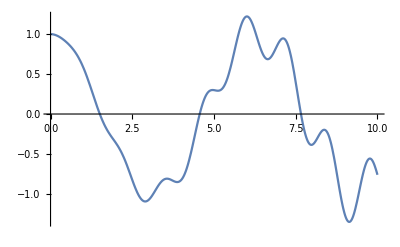

```mathematica
Plot[sol,{x,0,10}]
```

When using DSolve, you have to use /. to extract the solution expression:

```mathematica
sol = DSolve[{y''[x] == -y[x],y[0] ==1, y'[0] == 0},y[x],x]
```

{{y[x]→Cos[x]}}

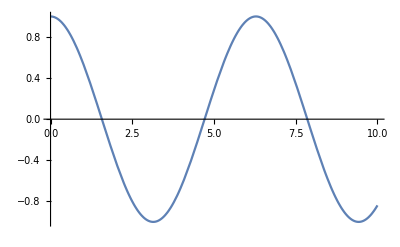

```mathematica
Plot[y[x]/. sol,{x,0,10}]
```

## Numerical Differential Equation Solving in Mathematica

The Mathematica function NDSolve is a general numerical differential equation solver.

#### Syntax

```mathematica
?NDSolve
```

```mathematica
sol = NDSolve[{y''[x] == -y[x],y[0] ==1, y'[0] == 0},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

NDSolve represents solutions for the functions x i as InterpolatingFunction objects.

In general, NDSolve finds solutions iteratively. It starts at a particular value of t_min, then takes a sequence of steps, trying eventually to cover the whole range t_min to t_max .

NDSolve has to be given appropriate initial or boundary conditions and the range of solution.

The initial or boundary conditions you give must be sufficient to determine a unique solution.

## NDSolve

#### Initial Value Problems

In a typical case, if you have differential equations with up to nth derivatives, then you need to
either give initial conditions for up to (n - 1)th derivatives, or give boundary conditions at n points.

This solves an initial value problem for a second-order equation, which requires two conditions,
and are given at t == 0 .

```mathematica
sol = NDSolveValue[{y''[x] == -y[x]^2 + Log[y[x]] + Cos[5x*y[x]],y[0] ==1, y'[0] == 0},y[x],{x,0,1}]
```

InterpolatingFunction[…][x]

This plots the solution obtained:

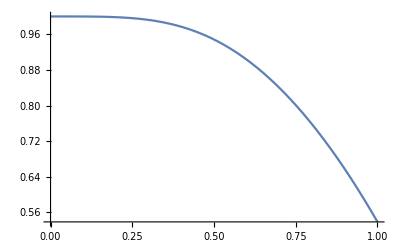

```mathematica
Plot[sol,{x,0,1}]
```

## NDSolve

#### Boundary Value Problems

In a typical case, if you have differential equations with up to nth derivatives, then you need to
either give initial conditions for up to (n - 1)th derivatives, or give boundary conditions at n points.

This plots the solution obtained:

Here is a simple boundary value problem.

InterpolatingFunction[…][x]

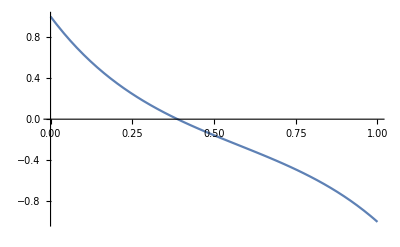

```mathematica
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1}]
Plot[sol,{x,0,1}]
```

## NDSolve

#### Coupled Systems of ODEs

You can use NDSolve to solve systems of coupled differential equations as long as each variable has the appropriate number of conditions.

x''[t]==x[t] y[t]

y'[t]==-1/(x[t]^2+y[t]^2)

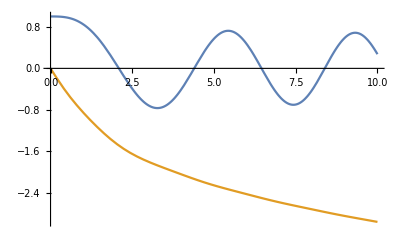

```mathematica
eq1 = x''[t]  == x[t] y[t]
eq2 = y'[t] == -1/(x[t]^2+ y[t]^2) 
bc1 = x[0] == 1; 
bc2 = x'[0] == 0;
bc3 = y[0] == 0; 
{X,Y} = NDSolveValue[{eq1,eq2,bc1,bc2,bc3},{x[t],y[t]}, {t,0,10}]; 
Plot[{X,Y},{t,0,10}]
```

## NDSolve

#### Differential-algebraic equations (DAEs)

Mixed systems of differential and algebraic equations are called  differential-algebraic equations (DAEs).

Here is a simple DAE.

y[t]+x''[t]==x[t]

x[t]^2+y[t]^2==1

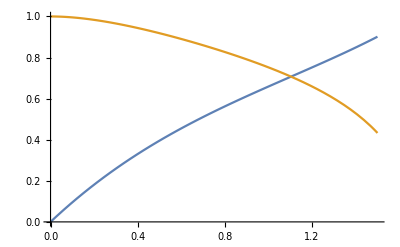

```mathematica
eq1 = x''[t] + y[t] == x[t]
eq2 = x[t]^2+ y[t]^2 == 1
bc1 = x[0] == 0; 
bc2 = x'[0] == 1;
{X,Y} = NDSolveValue[{eq1,eq2,bc1,bc2},{x[t],y[t]}, {t,0,1.5}]; 
Plot[{X,Y},{t,0,1.5}]
```

## NDSolve

#### Choosing a numerical method

NDSolve has several different methods built in for computing solutions.

With the default setting Method -> Automatic, NDSolve will choose a method which should be appropriate for the differential equations.

NDSolve will choose the write method and step size for you

```mathematica
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1},Method->"ImplicitRungeKutta"]
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1},Method->"Adams"]
```

InterpolatingFunction[…][x]

InterpolatingFunction[…][x]

## NDSolve

#### Choosing a numerical method

NDSolve has several different methods built in for computing solutions.

With the default setting Method -> Automatic, NDSolve will choose a method which should be appropriate for the differential equations.

NDSolve will choose the write method and step size for you

```mathematica
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1},Method->"ImplicitRungeKutta"]
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1},Method->"Adams"]
```

InterpolatingFunction[…][x]

InterpolatingFunction[…][x]

## NDSolve

#### Choosing a numerical method

NDSolve has several different methods built in for computing solutions.

With the default setting Method -> Automatic, NDSolve will choose a method which should be appropriate for the differential equations.

NDSolve will choose the write method and step size for you

```mathematica
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1},Method->"ImplicitRungeKutta"]
sol = NDSolveValue[{y''[x] == 10y[x] + 3Cos[x],y[0] ==1, y[1] == -1},y[x],{x,0,1},Method->"Adams"]
```

InterpolatingFunction[…][x]

InterpolatingFunction[…][x]

## NDSolve

#### Step Size

NDSolve will choose a step size the optimizes speed and accuracy at the same time.

The option MaxStepSize fixes the step size.

InterpolatingFunction[{{0., 2.}}, <>][x]

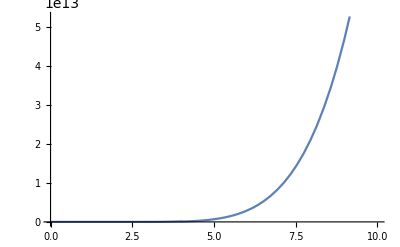

```mathematica
sol = NDSolveValue[{-y''[x] ==1Sin[x]+x y[x],y[0] ==1, y[1] == -1},y[x],{x,0,2},MaxStepSize->.00001]
Plot[sol,{x,0,10}]
```

The step-size can be visualized with  DifferentialEquations`NDSolveUtilties`

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"]
StepDataPlot[sol]
```

-Graphics-

## NDSolve

#### WhenEvent

WhenEvent specifies an action that occurs when the event triggers it for equations in NDSolvepaclet:ref/NDSolve and related functions.

Simulate a bouncing ball that retains 95% of its velocity in each bounce:

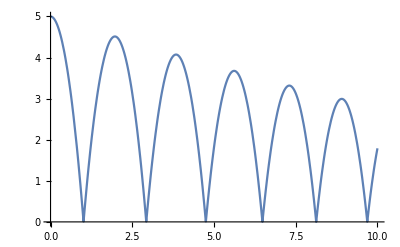

```mathematica
NDSolve[{y''[t]==-9.81,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.95y'[t]]},y,{t,0,10}];
Plot[y[t]/.%,{t,0,10}]
```

## Asymptotic Differential Equation Solving in Mathematica

## AsymptoticDSolveValue

Asymptotic approximations to differential equations are also known as asymptotic expansions, perturbation solutions, regular perturbations and singular perturbations

Asymptotic approximations are typically used to solve problems for which no exact solution can be found or to get simpler answers for computation, comparison and interpretation.

Find a series solution for a differential equation :

```mathematica
order = 3;
sol1 = AsymptoticDSolveValue[{y''[x]+Sin[x]y[x]==0,y[0]==1,y'[0]==0},y[x],{x,0,order}]
sol2 = NDSolveValue[{y''[x]+Sin[x]y[x]==0,y[0]==1,y'[0]==0},y[x],{x,0,3}]
```

1-x^3/6

InterpolatingFunction[…][x]

The

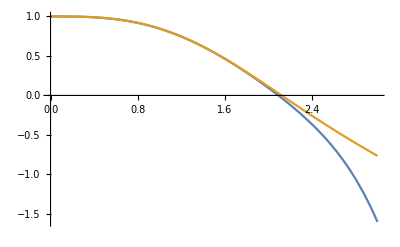

```mathematica
Plot[{sol1,sol2},{x,0,3}]
```

## Asymptotic Differential Equation Solving in Mathematica

## Perturbation problems

Find an asymptotic expansion for a perturbation problem:

ⅇ^-x-ⅇ^(-2 x) (-1+ⅇ^x) ϵ+ⅇ^(-3 x) (-1+ⅇ^x)^2 ϵ^2-ⅇ^(-4 x) (-1+ⅇ^x)^3 ϵ^3

InterpolatingFunction[…][x]

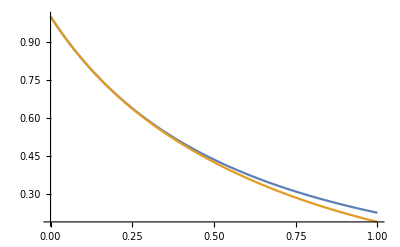

```mathematica
order = 3;
sol1 = AsymptoticDSolveValue[{ y'[x]+y[x]+ϵ y[x]^2==0, y[0]==1},y[x],x, {ϵ,0,order}]
sol2 = NDSolveValue[{ y'[x]+y[x]+y[x]^2==0, y[0]==1},y[x], {x,0,2}]

Plot[{sol2,Evaluate[Table[sol1,{ϵ,{1}}]]},{x,0,1}]
```